### Expanding on slides from: https://isapp2012paris.sciencesconf.org/conference/isapp2012paris/Stefano_Gabici_three.pdf

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

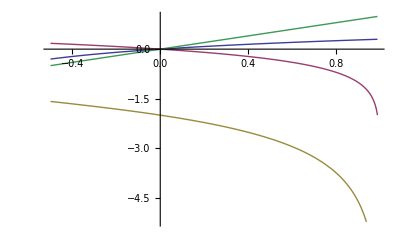

```mathematica
Needs["PlotLegends`"]
Plot[{Log10[1+x],Log10[1-x],-1 +(Log10[1-x]/Log10[1+x]),x},{x,-0.5,0.99},PlotLegend->{"log P","log β","Spectral Index","log/log"}]
```

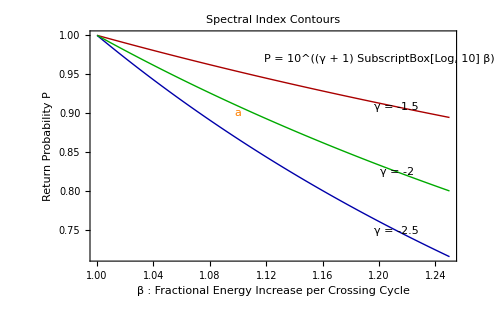

```mathematica
{minβ,maxβ,frac}={1,1.25,0.85};
fn[B_,a_]=10^((a+1)Log10[B]);
pows={-1.5,-2.5};
pows2={-1.5,-2,-2.5};
np=Length[pows];
imga=Show[
Plot[Evaluate[Table[fn[B,pows[[i]]],{i,np}]],{B,minβ,maxβ},
PlotStyle->{{Thick,Darker[Red]},{Thick,Darker[Blue]}},
(*Filling->{1->{{2},LightBlue}},*)
Epilog->{
Table[Inset[Framed[StringJoin["γ = ",ToString[pows2[[i]]]],RoundingRadius->5],{minβ +((maxβ-minβ)*frac),fn[minβ+((maxβ-minβ)*frac),pows2[[i]]]},Background->White],{i,3}],
Inset[Framed[StandardForm[Style["P = 10^((γ + 1) SubscriptBox[Log, 10] β)",18]],RoundingRadius->5],{1.2,0.97},Background->White],
{Orange,Text["a",{1.1,0.9}]}
}
],

Plot[fn[B,-2],{B,minβ,maxβ},PlotStyle->{Thick,Darker[Green]}],

Frame->True,
PlotLabel->Style["Spectral Index Contours",15],
FrameLabel->{
"β : Fractional Energy Increase per Crossing Cycle",
"Return Probability P"},
ImageSize->500
]
```

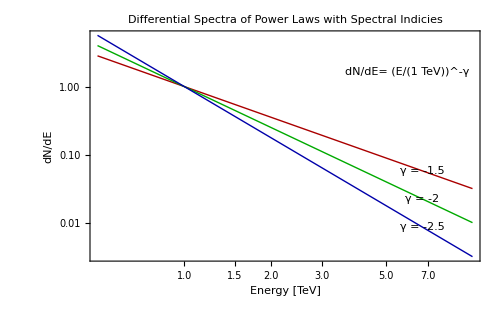

```mathematica
fn[x_,p_]=x^p;
pows2={-1.5,-2,-2.5};
imgb=LogLogPlot[{fn[x,-1.5],fn[x,-2],fn[x,-2.5]},{x,0.5,10},
Epilog->{
Table[Inset[Framed[StringJoin["γ = ",ToString[pows2[[i]]]],RoundingRadius->5],{Log10[80],Log10[fn[80,pows2[[i]]]]},Background->White],{i,3}],
Inset[Framed[StandardForm[Style["dN/dE="(("E")/("1" TeV))^-γ,15]],RoundingRadius->5],{Log10[60],Log10[3]},Background->White]
},
PlotStyle->{{Darker[Red],Thick},{Darker[Green],Thick},{Darker[Blue],Thick}},
Frame->True,
FrameLabel->{"Energy [TeV]",Rotate["dN/dE",-90°]},
PlotLabel->Style["Differential Spectra of Power Laws with Spectral Indicies",15],
ImageSize->500
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["blah.pdf",Magnify[GraphicsGrid[{{imga},{imgb}}],2]]
```

/Users/nkelhos/Dropbox/Research/Thesis/images/snr_shockfront

blah.pdf